# Adapted Tensor Renormalization Group

# ROUTINES

In this section we define and explain the different routines employed in the numerical protocol

### Parameters & Auxiliary routines

#### Parameters

The following are several parameters which affect global aspects of the algorithm

```mathematica
(*The protocol will truncate fields with associated eigenvalues λ<10^-MinimumValueExp*)
MinimumValueExp=11;
(*The protocol will use an approximate diagonalization routine (explained below) for the matrix B when one of the eigenvalues B is larger than 10^(2ApproximationExp)*)
ApproximationExp=2.5;
(*The protocol will check for possible numerical errors ϵ in different places and print an alert if ϵ>10^-PrintErrorExp*)
PrintErrorExp=6;
(*If PrintText=False, no intermediate information is printed, the only exception are error messages. If PrintTensor=True, show at each step the block structure of the tensors involved in the interaction up to order PrintTensorOrder.*)
PrintText=False; 
PrintTensor=False; PrintTensorOrder=4;
```

#### Auxiliary routines

The following routines are convenient shortcuts

```mathematica
(*Substitution for "Print" that only prints if PrintText=True*)
Pri[x__]:=If[PrintText,Print@@List[x]];
(*Cast time variable t in a more readable format, used in the quantification of computation time spent in some routines*)
TimeToString[t_]:=ToString[Floor[t/3600]]<>":"<>ToString[Mod[Floor[t/60],60]]<>":"<>ToString[Round[Mod[t,60]]];
```

The following routines give the exact computation of the free energy per site for the λϕ^4 theory at first order in perturbation theory

```mathematica
(*Auxiliary quantity*)
EVFE[m_,order_,nt_,nx_]:=4 Sin[(nt Pi)/2^order]^2+4 Sin[(nx Pi)/2^order]^2+m^2//N;
(*Order O(λ^0) for a lattice of L=2^order sites per side and mass m*)
ExactFE0[m_,order_]:=-(1/2 Log[2Pi]-1/2^(2order+1)Sum[Log[EVFE[m,order,nt,nx]]//N,{nt,2^order},{nx,2^order}]//N);
(*Order O(λ^0) for a lattice of L->∞ sites per side, which correspond to the continuum limit, and mass m*)
ExactContFE0[m_]:=-(1/2 Log[2Pi]-1/2 NIntegrate[Log[4 Sin[t Pi]^2+4 Sin[x Pi]^2+m^2]//N,{t,0,1},{x,0,1}]//N);
(*Order O(λ^0) for a lattice of L->∞ sites per side and mass m=0, which correstpond to the continuum massless limit*)
fexml=1/2 Log[2Pi]-2/Pi Catalan//N;
(*Order O(λ^1) for a lattice of L=2^order sites per side and mass m*)
ExactFE1[m_,order_]:=3Sum[1/(2^(2order)EVFE[m,order,nt,nx])//N,{nt,2^order},{nx,2^order}]^2//N;
(*Order O(λ^1) for a lattice of L->∞ sites per side, which correstpond to the continuum limit, and mass m*)
ExactContFE1[m_]:=3NIntegrate[1/(4 Sin[t Pi]^2+4 Sin[x Pi]^2+m^2)//N,{t,0,1},{x,0,1}]^2//N;
```

### Adapted TRG main routine

The following routine is the main one. It implements the adapted Tensor Renormalization Group protocol. 
Its input values are:
 -> m is thee mass of the boson field
  -> order fixes the size of the lattice, which has L=2^order sites per side
 -> fields is the bond dimension χ. At the steps where a larger number of fields appear, only fields of them will be maintained, the rest will be truncated.
Its output values are:
 -> the free energy per site at order 0 and 1 in perturbation theory
  -> information about some intermediate variables (not necessary, but useful for a more detailed analysis of the protocol)
This routine structures the algorithm. It sets the initial Boltzmann weights before the first step and makes use of the routines corresponding to one step of the adapted TRG to actualize those weights the number of times it is required in order to compute the free energy of the whole lattice.

```mathematica
TRG[m_,order_,fields_]:=Module[{a1,d,ds,ua1,ub1,q,qs,fes,fex,fin,TV,t,H,s,ro,secs},

(*Set the initial values of the matrices at the exponent (see notes for more information)*)
(*Eigenvalues of B (the first set depending on the mass is just added for convenience, as a way to represent the exponent in a more compact fashion, they will be discarded latter, at the end of the section named Order 0):*)
ds={{If[m==0,Infinity,m^-2]},{1,1}}//N; 
(*Block matrices of A and U:*)
a1=ua1=ub1={{1}}//N;
(*Eigenvalues of Q:*)
qs={};

(*Set the initial values of the tensor with the coefficients of the interaction part (see notes for more information). Functions TNew and TSet are defined in the section named Order 1*)
(*Create new empty tensor*)
TV=TNew[4,{2,2,2}];
(*Create new empty block of x^4 variables*)
t=ConstantArray[0,{2,2,2,2}];
(*Set the block to -(Subscript[x, 1]^4+Subscript[x, 2]^4)/2*)
t[[1,1,1,1]]=t[[2,2,2,2]]=-.5;
(*Get the block into the tensor*)
TV=TSet[TV,t,{0,4,0}];

(*Loop over the adapted TRG step*)
For[s=1,s≤2(order-1),s++,
(*Print information about this step*)
Pri[Style["Step "<>ToString[s]<>"/"<>ToString[2order-1],Bold]];
(*Compute one adapted TRG step, getting the computation time*)
secs=Timing[
(*Routine for the actualization of variables after one step (defined below, in the section named Order 0)*)
{a1,ua1,ub1,d,q,TV}=RegularStep[a1,ua1,ub1,ds[[-2]],ds[[-1]],TV,fields,s]//N;
(*Store some of the variables resulting of this step*)
AppendTo[ds,d];AppendTo[qs,q];
][[1]];
(*Print information about computation time*)
Pri[Style["Δt = "<>TimeToString[secs],Italic]];
];

(*Print information about the final step*)
Pri[Style["Final step "<>ToString[s]<>"/"<>ToString[2order-1],Bold]];
(*Compute the final step, getting the computation time*)
secs=Timing[
(*The final step is different. We have to compute the trace of the Boltzmann weight. We use the information stored in ds and qs to compute the final value of the free energy fes. This routine is defined below, in the section named Order 0*)
{fes,q}=FinalStep[a1,ua1,ub1,ds,qs,TV,fields,order]//N;(*Store some of the variables resulting of this step*)
AppendTo[qs,q];
][[1]];
(*Print information about computation time*)
Pri[Style["Δt = "<>TimeToString[secs],Bold]];

(*The result of the algorithm is the free energy fes=(Subscript[f, 0],Subscript[f, 1]) *)
fes
];
```

### Order 0 routines

The following routines compute the change of the matrices in the exponential of a Boltzmann weight after one iteration of the adapted TRG protocol.

#### Auxiliary routines

The routines in this section are auxiliary. They are called from the main order 0 routines defined in the following sections

```mathematica
(*Compute the (Hilbert–Schmidt) matrix norm, normalized by the number of variables*)
MatrixNorm[M_]:=Sqrt[Tr[M.ConjugateTranspose[M]]]/Length[M];

(*Compute the symmetrized version of a matrix*)
Sym[M_]:=1/2(M+Transpose[M]);

(*Approximate diagonalization of a matrix B with form B=ϵ^-1 Subscript[v, 0].Subscript[v, 0]^T+Subscript[B, 0], with Subscript[v, 0]^T.Subscript[v, 0]=1. We expand the diagonalization, computing the eigenvalues and eigenvectors of B up to second order in ϵ. The inputs are ϵ, Subscript[v, 0] and Subscript[B, 0], and the information {step, label} used for printing alerts. The outputs are the eigenvalues and eigenvectors of the approximate diagonalization*)
ApproximateDiagonalization[ϵin_,v0in_,B0in_,step_,label_]:=Module[{P,ϵp,v0p,B0p,ϵ,v0,B0,n,W,B0t,V0,λ0s,error,c,cs,css,ds,dss,λ,λs,v,V},

(*Define useful quantities (see notes for more information)*)
P=IdentityMatrix[Length[v0in]]-v0in.Transpose[v0in];
ϵ=(ϵin^-1+(Transpose[v0in].B0in.v0in)[[1,1]])^-1;
v0=v0in+ϵin P.B0in.v0in;
B0=P.(B0in-ϵ B0in.v0in.Transpose[v0in].B0in).P;
ϵ=ϵ/Norm[v0[[All,1]]]^2//N;
v0=Transpose[{Normalize[v0[[;;,1]]]}]//N;
(*dimension of the orthogonal space to Subscript[v, 0]*)
n=Length[v0]-1;
(*projector onto the orthogonal space to Subscript[v, 0]*)
W=Transpose[Normalize/@Eigenvectors[IdentityMatrix[n+1]-v0.Transpose[v0]][[;;-2]]];
(*Define quantities (see notes for more information)*)
B0t=Transpose[W].B0.W//Sym;
V0=W.Transpose[Normalize/@Eigenvectors[B0t]];λ0s=Eigenvalues[B0t];
(*Check errors. If the error is too big, print an alert.*)
error=Abs[MatrixNorm[Transpose[W].V0.DiagonalMatrix[λ0s].Transpose[V0].W-B0t]]//N;
If[error>10^-PrintErrorExp,Print["Approx (",label,") diagonalization error = ",error,", ","step=",step]];
(*Define and compute coefficients (see notes for more information)*)
c=(Transpose[v0].B0.v0)[[1,1]]//N;
cs=Table[(Transpose[V0[[;;,{k}]]].B0.v0)[[1,1]],{k,n}]//N;
css=Table[If[l==k,0,(cs[[l]]cs[[k]])/(λ0s[[l]]-λ0s[[k]])],{l,n},{k,n}]//N;
ds=Table[cs[[k]](c-λ0s[[k]])-Sum[If[l==k,0,css[[l,k]]cs[[l]]],{l,n}],{k,n}]//N;
dss=Table[If[l==k,0,(cs[[k]]^2 css[[l,k]]+cs[[l]]ds[[k]])/(λ0s[[l]]-λ0s[[k]])],{l,n},{k,n}]//N;
(*Compute main eigenvalue*)
λ=1/ϵ+c+ϵ Sum[cs[[l]]^2,{l,n}]//N;
(*Compute other eigenvalues*)
λs=Table[λ0s[[k]]-ϵ cs[[k]]^2+ϵ^2cs[[k]]ds[[k]],{k,n}]//N;
(*Compute main eigenvector*)
v=(1-ϵ^2/2 Sum[cs[[l]]^2,{l,n}])v0
+ Sum[(ϵ cs[[l]]+ϵ^2(λ0s[[l]]-c)cs[[l]] ) V0[[;;,{l}]],{l,n}]//N;
(*Compute other eigenvectors*)
V=Transpose[Table[
(1-ϵ^2 1/2(cs[[k]]^2+Sum[css[[l,k]]^2,{l,n}]))V0[[;;,k]]
+(-ϵ cs[[k]]+ϵ ^2 ds[[k]] )v0[[;;,1]]
+Sum[(ϵ css[[l,k]]-ϵ^2 dss[[l,k]])V0[[;;,l]],{l,n}]
,{k,n}]]//N;
(*Check errors. If the error is too big, print an alert.*)
error=Abs[MatrixNorm[Transpose[V].V-IdentityMatrix[n]]]//N;
If[error>10^-PrintErrorExp,Pri["Approx. (",label,") normalization error = ",error,", ","step=",step]];
If[ϵ λ0s[[1]]>0.1,Pri["Approx. (",label,") ϵ max(λ0s) = ", ϵ λ0s[[1]],", ","step=",step]];
(*Result: approximate eigenvalues and eigenvectors*)
{Re[Join[{λ},λs]],Join[v,V,2]}//N
]

(*Check if the matrix b needs a regular Mathematica diagonalization or an approximate diagonalization (defined in the previous routine), and then compute it. Information {step, label} is used for printing alerts.*)
TryApproxDiag[b_,step_,label_]:=Module[{d,u,error,ϵ,v0,B0},
(*Compute regular Mathematica eigenvalues d and eigenvectors u*)
d=Eigenvalues[b//Sym]//N;u=Transpose[Eigenvectors[b//Sym]]//N;
(*Check if the biggest eigenvalue or the diference among it and the second is too big. If one of them is, then use the approximate diagonalization.*)
If[Abs[1/d[[1]]]>(10^-ApproximationExp)^2||Abs[Divide@@d[[1;;2]]]<100,
(*Not using approximation*)
(*Check errors.If the error is too big,print an alert.*)
error=Abs[MatrixNorm[u.DiagonalMatrix[d].Transpose[u]-b]]//N;
If[error>10^-PrintErrorExp,Pri["Diagonalization error (",label,") = ",error,", ","step=",step]];
,
(*Using approximation*)
(*Express the matrix b in the form b=ϵ^-1 Subscript[v, 0].Subscript[v, 0]^T+Subscript[B, 0]. Compute the different quantities.*)
ϵ=1/d[[1]]//N;
v0=u[[;;,{1}]];
ϵ=ϵ/Norm[v0[[All,1]]]^2//N;
v0=Transpose[{Normalize[v0[[;;,1]]]}]//N;
B0=b-v0.Transpose[v0]/ϵ//N;
(*Compute the approximate diagonalization of b to get the eigenvalues d and eigenvectors u*)
{d,u}= ApproximateDiagonalization[ϵ,v0,B0,step,label]//N; 
];
(*Result: eigenvalues and eigenvectors*)
{d,u}
];
```

#### Regular step

This routine performs one step of the adapted TRG protocol. 
It takes as inputs:
 -> The blocks defining matrices A and U (a1, ua1, ub1)
 -> The eigenvalues of B at the present step (d1) and at the previous one (d0)
 ->  The array of tensors with the coefficients of the interaction part (TV1)
  -> The bond dimension (number of fields admitted before truncation)
  -> The number of the present step
Its outputs are:
 -> The new blocks of A and B  (a2, ua2t, ub2t)
 -> The eigenvalues of B (db) and Q (q)
 ->  The tensor with the new coefficients of the interaction part (TV2)

```mathematica
RegularStep[a1_,ua1_,ub1_,d0_,d1_,TV1_,fields_,step_]:=Module[{qa,qb,qc,q,qai,qbi,qci,a2,ba,bb,ua2,ub2,ua2t,ub2t,da2,db2,error,p,ϵ,v0,daux,B0,ϵp,v0p,B0p,P,dab,r,ra,rb,h,g,cp,cm,TV2,H2,cdlexp,cdlpot,d2},

(*Matrix Q*)
(*Definition of the blocks of Q (see notes for more information)*)
qa=DiagonalMatrix[1/d0]+2a1//N;qb=DiagonalMatrix[1/d0]//N;qc=DiagonalMatrix[1/d0]+4a1//N;
(*q are the eigenvalues of Q*)
q=Eigenvalues[qa]//N;q=Join[1/d0,q,q,Eigenvalues[qc]]//N;
(*Compute the inverse of the blocks of Q*)
qai=Inverse[qa]//N;qbi=DiagonalMatrix[d0]//N;qci=Inverse[qc]//N;
(*Check the precision of the inversion and if it is too poor print an alert*)
error=Abs[MatrixNorm[qa.qai-IdentityMatrix[Length[qa]]]+MatrixNorm[qc.qci-IdentityMatrix[Length[qc]]]]//N;
If[error>10^-PrintErrorExp,Print["Inverse error = ",error,", ","step=",step]];

(*Matrices A and B*)
(*Definition of the blocks of A (see notes for more information)*)
a2=1/2 ArrayFlatten[({{Transpose[ua1]}, {-Transpose[ub1]}})].qai.Transpose[ArrayFlatten[({{Transpose[ua1]}, {-Transpose[ub1]}})]]//N;
(*Definition of the blocks of B (see notes for more information)*)
ba=1/2 ArrayFlatten[({{Transpose[ua1]}, {Transpose[ub1]}})].qai.Transpose[ArrayFlatten[({{Transpose[ua1]}, {Transpose[ub1]}})]]//N;
bb=1/2 ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})].ArrayFlatten[({{2qbi-qai, qai}, {qai, 2qci-qai}})].Transpose[ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})]]//N;
(*Diagonalize ba using the approximate diagonalization routine if necessary. da2 are the eigenvalues, ua2 the matrix of (column) eigenvectors. TryApproxDiag is defined in the section named Auxiliary routines*)
{da2,ua2}=TryApproxDiag[ba,step,"b1"];
(*Diagonalize bb. This diagonallization is more complicated since for small mases bb can have one very large eigen value.*)
(*Get the position of the largest contribution to bb*)
p=Position[d0,Max[d0]][[1,1]];
(*Find if this contribution is not large enough or if the the proportion of the two larger eigenvalues is not too large*)
If[Abs[1/d0[[p]]]>(10^-ApproximationExp)^2||Abs[Divide@@Eigenvalues[bb][[1;;2]]]<100,
(*If the conditions for the approximation are not satisfied, perform a normal diagonalization*)
(*Find if ua1 and ub1 are square matrices*)
If[Length[qa]==Length[ua1[[1]]],
(*If ua1 and ub1 are square matrices, we can save a change of basis by taking into account that U is an orthogonal matrix.*)
(*Eigenvalues of bb*)
db2=1/2 Eigenvalues[ArrayFlatten[({{2qbi-qai, qai}, {qai, 2qci-qai}})]]//N;
(*Matrix of (column) eigenvectors of bb*)
ub2=ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})].Transpose[Eigenvectors[ArrayFlatten[({{2qbi-qai, qai}, {qai, 2qci-qai}})]]]//N;
,
(*If ua1 and ub1 are not square matrices, use the normal diagonalization routines.*)
(*Eigenvalues of bb*)
db2=Eigenvalues[bb//Sym];
(*Matrix of (column) eigenvectors of bb*)
ub2=Transpose[Eigenvectors[bb//Sym]];
];
(*Check the precision of the diagonalization and if it is to poor print an alert*)
error=Abs[MatrixNorm[ub2.DiagonalMatrix[db2].Transpose[ub2]-bb]]//N;
If[error>10^-PrintErrorExp,Pri["Diagonalization error (b) = ",error,", ","step=",step]];
,

(*If the above conditions for the approximation are satisfied, use the approximate diagonalization routine. Our matrix have the form B=ϵ^-1 Subscript[v, 0].Subscript[v, 0]^T+Subscript[B, 0], with Subscript[v, 0]^T.Subscript[v, 0]=1, we want to expand its diagonalization in series of ϵ*)
(*Define the parameters of the approximate diagonalization (see notes for more information)*)
(*Define ϵ and Subscript[v, 0]*)
ϵ=1/d0[[p]]//N;
v0=ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})][[;;,{p}]]//N;
ϵ=ϵ/Norm[v0[[All,1]]]^2//N; (*expansion parameter*)
v0=Transpose[{Normalize[v0[[;;,1]]]}]//N;
(*Define Subscript[B, 0]*)
daux=d0;
daux[[p]]=0;
B0=1/2 ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})].ArrayFlatten[({{2DiagonalMatrix[daux]-qai, qai}, {qai, 2qci-qai}})].Transpose[ArrayFlatten[({{Transpose[ua1], 0}, {0, Transpose[ub1]}})]]//N;
(*Apply the approximate diagonalization*)
{db2,ub2}= ApproximateDiagonalization[ϵ,v0,B0,step,"b2"]//N; 
];

(*Truncation of fields. If there are more fields than the bond dimension χ, or if some of the fields have an associated eigenvalue too small (<10^-MinimumValueExp), this part of the algorithm will truncate them.*)
(*Join all eigenvalues of the present step*)
dab=Join[da2,db2];
(*Find the number of fields r we will not truncate.*)
r=Min[fields,Count[dab,x_/;Re[x]>10^-MinimumValueExp]];
(*We only allow an even number of fields (the two blocks da and db must have the same dimension)*)
If[OddQ[r],r-=1];
(*Get the positions of the largest eigenvalues (ra corresponds to da and rb to db)*)
ra={};rb={};
Table[If[k≤Length[da2],AppendTo[ra,k],AppendTo[rb,k-Length[da2]]],{k,Reverse[Ordering[dab]][[;;r]]}]//N;
(*Apply the truncation. We only maintain fields at positions ra and rb*)
(*New set of eigenvalues*)
d2=Join[da2[[ra]],db2[[rb]]]//Re;
(*New blocks of the matrix U with truncated entries*)
ua2t=ua2[[;;,ra]];ub2t=ub2[[;;,rb]];

(*Use the routines defined in the section named Order 1 to perform the computations at the level of the interaction part. TV1 is the old tensor with the information at the interaction part, from the begining of the present adapted TRG step. TV2 is the new tensor at the end of the step. cdlpot carries information about the CDL structure at the level of the interaction part.*)
{TV2}=TRegularStep[TV1,a1,ua1,ub1,ua2t,ub2t,qa,qb,qc,qai,qbi,qci,d0,d1];

(*Results*)
{a2//Sym,ua2t,ub2t,d2,q,TV2}
];
```

#### Final step

This routine performs the final step of the adapted TRG protocol and also adds all the contributions from the previous steps to get the final result. 
It takes as inputs:
 -> The blocks defining matrices A and U (a1, ua1, ub1)
 -> The eigenvalues of B and Q at all the steps (dall and qall)
 ->  The tensor with the coefficients of the interaction part (TV1)
  -> The bond dimension (number of fields admitted before truncation)
   -> The order of the lattice order, which gives the number of sites of the lattice
Its outputs are:
 -> The free energy at order 0 fe0 and at order 1 fe1 in λ
 -> The eigenvalues of the final matrix Q (q)

```mathematica
FinalStep[a1_,ua1_,ub1_,dall_,qall_,TV1_,fields_,order_]:=Module[{ds,qs,d0,d1,qa,qb,qc,q,qai,qbi,qci,ba,bb,a2,ua2,ub2,da2,db2,r,error,up,um,Q,fe0,fe1},

(*Compute the contribution of the final step, given by the conraction of all fields (see notes for more information)*)
(*Rename list of eigenvalues to append the new ones*)
ds=dall;qs=qall;
(*Get the eigenvalues from the last two steps*)
d0=ds[[-2]];d1=ds[[-1]];
(*Compute the blocks of Q*)
qa=DiagonalMatrix[1/d0]+2a1//N;qb=DiagonalMatrix[1/d0]//N;qc=DiagonalMatrix[1/d0]+4a1//N;
(*Compute the eigenvalues of Q*)
q=Eigenvalues[qa]//N;q=Join[1/d0,q,q,Eigenvalues[qc]]//N;
(*Add the new eigenvalues of Q to the list of eigenvalues from the previous steps*)
AppendTo[qs,q];
(*Compute the inverse of the blocks of Q*)
qai=Inverse[qa]//N;
qbi=DiagonalMatrix[d0]//N;
qci=Inverse[qc]//N;
(*Compute final matrix Q. This is the matrix with all the information of the exponent just before the integration of all the remaining variables. Its determinant will be the last contribution to the free energy.*)
Q=DiagonalMatrix[1/Join[d1,d1]]+2ArrayFlatten[({{Transpose[ua1], 0, 0, 0}, {0, Transpose[ub1], 0, 0}, {0, 0, Transpose[ua1], 0}, {0, 0, 0, Transpose[ub1]}})].ArrayFlatten[({{qai, 0, 0, 0}, {0, qci, 0, qci}, {0, 0, qai, 0}, {0, qci, 0, qci}})].Transpose[ArrayFlatten[({{Transpose[ua1], 0, 0, 0}, {0, Transpose[ub1], 0, 0}, {0, 0, Transpose[ua1], 0}, {0, 0, 0, Transpose[ub1]}})]]//N;

(*Compute the final result for the free energy*)
(*The first set of eigenvalues was just added for convenience in the TRG routine, now we discard them*)
ds=Drop[ds,1];
(*Add all the contributions to the free energy at order 0 in λ. The contribution of one tensor at one step is multiplied by the number of tensors at that step.*)
fe0=-(1/2 Log[2Pi]-Sum[2^(-k-2)(2Total[Log[ds[[k]]]]+Total[Log[qs[[k]]]]),{k,Length[ds]}]-2^(-2order-1)Log[Abs[Det[Q]]]);
(*Use the routines defined in the section named Order 1 to compute the first order correction to the free energy*)
fe1=- TFinalStep[TV1,a1,ua1,ub1,qa,qb,qc,qai,qbi,qci,d0,d1];

(*Final result*)
{{fe0,fe1},q}//N
];
```

### Order 1 routines

The following routines compute the change of the quantities at the level of the interaction part of a Boltzmann weight after one iteration of the adapted TRG protocol.

#### Auxiliary routines

The routines in this section are auxiliary. They are called from the main order 1 routines defined in the following sections. Their main purpose is to store and handle the coefficients of the polynomial function f that defines the interaction part of a Boltzmann weight in an efficient way. The polynomial function depends on three kind of variables, namely d_x, x and d_y. In order to simplify the notation, we will renamed them to, respectively, x, y and z.
In order to handle the polynomial f(x,y,z) in a practical way we use an object T_(j k l), which is an order=3 array. Each entry of the array T_(j k l) is the tensor t of order=j+k+l corresponding to the elements in f(x,y,z) with the form x^j*y^k*z^l. For example, let say we want to get from T the complex coefficient c of the monomial in f with the form  x_a x_b y_c z_d. Then we have to obtain the order=4 tensor t=T_(2 ,1 ,1) corresponding to power-2 in x and power-1 in y and z. After that, we have to obtain from it the specific element t_(a b c d).
However, the object T can be further optimized. Since all tensors t with odd order order=j+k+l have all elements equal to zero, we can just omit them. Similarly, the elements with total power j+k+l larger than the order of the polynomial will be always zero. Furthermore, by the structure of the protocol we know that all coefficients are always real or pure imaginary. Hence, we can only use real variables if we store the corresponding information in two different objects. The first one T stores all the coefficients of f  as we have explained above, but as real variables. The second object T’ is an array that stores one complex coefficient c with |c|=1 for each entry t of T. The actual tensor of coefficients is given by c*t.
We will call T0 (or T1) the object T0={T’,T} containing the array of coefficients T’ and the array of tensors T. 
The following routines are the only ones which directly access the elements in T0. They are the building blocks for the rest of routines in this section.

```mathematica
(*Construct a new symmetric tensor T0 of rank r and dimensions {d1,d2,d3} with entries equal to zero*)
TNew[r_,{d1_,d2_,d3_}]:=Module[{T0,pt},
{
(*The first entry gives the array of complex coefficients. Their value has to be a power of I. A convenient choice is I^p3, but it does not affect the final result.*)
Table[
(*Entry corresponding to powers {p1,p2,p3} of the three variables {x,y,z}. pt is the total power.*)
pt=p1+p2+p3;
(*Only set to some value different from zero the useful entries (the ones up to the order of the polynomial and even)*)
If[pt≤r&&EvenQ[pt],I^p3,0]
,{p1,0,r},{p2,0,r},{p3,0,r}]
,
(*The second entry gives the array of tensors.*)
Table[
(*Entry corresponding to powers {p1,p2,p3} of the three variables {x,y,z}. pt is the total power.*)
pt=p1+p2+p3;
(*Only set to some value different from zero the useful entries (the ones up to the order of the polynomial and even)*)
If[pt≤r&&EvenQ[pt],ConstantArray[0,Join[ConstantArray[d1,p1],ConstantArray[d2,p2],ConstantArray[d3,p3]]],0]
,{p1,0,r},{p2,0,r},{p3,0,r}]
}
];

(*Get the tensor of powers {p1,p2,p3} from T0*)
TGet[T0_,{p1_,p2_,p3_}]:=T0[[2,p1+1,p2+1,p3+1]];
(*Get the coefficient of powers {p1,p2,p3} from T0*)
TCoefGet[T0_,{p1_,p2_,p3_}]:=T0[[1,p1+1,p2+1,p3+1]];

(*Set to t the tensor of powers {p1,p2,p3} in T0*)
TSet[T0_,t_,{p1_,p2_,p3_}]:=Module[{T1},T1=T0;T1[[2,p1+1,p2+1,p3+1]]=t;T1];
(*Set to c the coefficient of powers {p1,p2,p3} in T0*)
TCoefSet[T0_,c_,{p1_,p2_,p3_}]:=Module[{T1},T1=T0;T1[[1,p1+1,p2+1,p3+1]]=c;T1];

(*Get the maximum rank of the tensors in T0*)
TRank[T0_]:=Length[T0[[2]]]-1;

(*Dimensions of the vectors of variables {x,y,z} in T0*)
TDims[T0_]:={Length[TGet[T0,{1,1,0}]],Length[TGet[T0,{0,1,1}]],Length[TGet[T0,{1,0,1}][[1]]]};

(*Multiply T0 by a coefficient*)
TTimes[T0_,c_]:={T0[[1]],c T0[[2]]};
```

The following routines use the previous ones to implement specific computations on T0 which will be needed in the following sections.

```mathematica
(*Sum two arrays*)
TSum[T1_,T2_]:=Module[{Tn,r,pt,t,s},
(*Initialize the array were we will store the result*)
Tn=T1;
(*Order of the tensors*)
r=TRank[T1];
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power.*)
pt=px+py+pz;
(*Run over the useful entries (the ones up to the order of the polynomial and even)*)
If[pt≤r&&EvenQ[pt],
(*We have to take into account the relation among the coefficients of T1 and T2, then we can sum the corresponding tensors.*)
s=TCoefGet[T2,{px,py,pz}]/TCoefGet[T1,{px,py,pz}]//Chop;
t=TGet[T1,{px,py,pz}]+s TGet[T2,{px,py,pz}];
(*Set the resulting tensor in its place in Tn*)
Tn=TSet[Tn,t,{px,py,pz}];
];
,{px,0,r},{py,0,r},{pz,0,r}];
(*Result*)
Tn
];

(*Print the tensors inside T0 up to order o*)
TPrint[T0_,o_]:=Module[{t,pt},
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power.*)
pt=px+py+pz;
(*Run over the useful entries (the ones up to the order of the polynomial and even)*)
If[pt≤o&&EvenQ[pt],
(*Print the tensor corresponding to powers {px,py,pz} (recall that the three variables are {x,y,z} in the program are {Subscript[d, x],x,Subscript[d, p]} in the notes)*)
Pri["T(d_x^",px,",x^",py,",d_p^",pz,") = ",TCoefGet[T0,{px,py,pz}],"*",MatrixForm@Chop@TGet[T0,{px,py,pz}]];
];
,{px,0,o},{py,0,o},{pz,0,o}];
];

(*Symmetrize the tensors inside T0*)
TSym[T0_]:=Module[{T,r,pt,t},
T=T0;
(*Order of the tensors*)
r=TRank[T];
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power.*)
pt=px+py+pz;
(*Run over the useful entries (the ones up to the order of the polynomial and even)*)
If[pt>0&&pt≤r&&EvenQ[pt],
(*Get the tensor corresponding to powers {px,py,pz}*)
t=TGet[T,{px,py,pz}];
(*symmetrice t with respect to x*)
t=Sum[
Transpose[t,Join[pi,px+Range[py],px+py+Range[pz]]]
,{pi,Permutations[Range[px]]}]/Factorial[px];
(*symmetrice t with respect to y*)
t=Sum[
Transpose[t,Join[Range[px],px+pi,px+py+Range[pz]]]
,{pi,Permutations[Range[py]]}]/Factorial[py];
(*symmetrice t with respect to z*)
t=Sum[
Transpose[t,Join[Range[px],px+Range[py],px+py+pi]]
,{pi,Permutations[Range[pz]]}]/Factorial[pz];
(*Set the new tensor in its place*)
T=TSet[T,t,{px,py,pz}];
];
,{px,0,r},{py,0,r},{pz,0,r}];
(*Result*)
T
];

(*Apply the change of basis U for the set of variables with number v, with v={1,2,3} (corresponding to {x,y,z})*)
TCB[T0_,U_,v_]:=Module[{r,no,nn,T1,t,pt},
(*Get the order of the tensors*)
r=TRank[T0];
(*Get dimensions of U*)
{no,nn}=Dimensions[U];
(*Initialize T1, where we will store the new tensors*)
T1=T0;
Which[
(*Aply the change of basis to the first set of variables*)
v==1,
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power. Run over the useful entries (the ones up to the order of the polynomial and even)*)
pt=px+py+pz;
If[pt≤r&&EvenQ[pt],
(*Get the tensor corresponding to powers {px,py,pz}*)
t=TGet[T0,{px,py,pz}];
(*Substitute x->U.x for the first x and position it at the end of the xs. Repeat the process for each x*)
Table[
t=Table[Sum[t[[k1]]U[[k1,k2]],{k1,no}],{k2,nn}];
t=Transpose[t,Join[{px},Range[1,px-1],Range[px+1,pt]]];
,px];
(*Set the new tensor in its place*)
T1=TSet[T1,t,{px,py,pz}];
];
,{px,1,r},{py,0,r},{pz,0,r}];

(*Aply the change of basis to the second set of variables*)
,v==2,
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power. Run over the useful entries (the ones up to the order of the polynomial and even)*)
pt=px+py+pz;
If[pt≤r&&EvenQ[pt],
(*Get the tensor corresponding to powers {px,py,pz}*)
t=TGet[T0,{px,py,pz}];
(*Substitute y->U.y for the first y and position it at the end of the ys. Repeat the process for each y*)
Table[
t=Transpose[t,Join[Range[2,px+1],{1},Range[px+2,pt]]];
t=Table[Sum[t[[k1]]U[[k1,k2]],{k1,no}],{k2,nn}];
t=Transpose[t,Join[{px+py},Range[1,px+py-1],Range[px+py+1,pt]]];
,py];
(*Set the new tensor in its place*)
T1=TSet[T1,t,{px,py,pz}];
];
,{px,0,r},{py,1,r},{pz,0,r}];

(*Aply the change of basis to the third set of variables*)
,v==3,
Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power. Run over the useful entries (the ones up to the order of the polynomial and even)*)
pt=px+py+pz;
If[pt≤r&&EvenQ[pt],
(*Get the tensor corresponding to powers {px,py,pz}*)
t=TGet[T0,{px,py,pz}];
(*Substitute z->U.z for the first z and position it at the end of the zs. Repeat the process for each z*)
Table[
t=Transpose[t,Join[Range[2,px+py+1],{1},Range[px+py+2,pt]]];
t=Table[Sum[t[[k1]]U[[k1,k2]],{k1,no}],{k2,nn}];
t=Transpose[t,Join[{pt},Range[1,pt-1]]];
,{p,pz}];
(*Set the new tensor in its place*)
T1=TSet[T1,t,{px,py,pz}];
];
,{px,0,r},{py,0,r},{pz,1,r}];
];
(*Result*)
T1
];
```

The following routine performs the main part of the work of the adapted TRG protocol at the level of the interaction part. It takes an array of tensors T0 depending on variables {d_x, x, d_y} and outputs the corresponding array of tensors at the next step T1, depending on variables {d_y, y, d_z}. For clarity reasons, we will rename these sets of variables to {x, y, z} and {z, u, v} respectively. Explicitly, this routine takes as inputs:
 -> The array of tensors T0 (depending on variables {x, y, z})
 -> The set of matrices matcoefs which specify the transformation from T0 to T1
Its outputs are:
 -> The array of tensors T1 (depending on variables {z, u, v})
matcoefs contains one set of coefficients (which are of the form c_(a,b)=I^n) and one set of matrices  U_(a,b). The routine compute all possible Feynman diagrams by performing the following substitutions (see notes for more information):
+c_(x,u)U_(x,u).u+c_(x,v)U_(x,v).v for each not contracted x.
+c_(y,u)U_(y,u).u+c_(y,v)U_(y,v).v for each not contracted y.
+c_(x,x)U_(x,x) for each contraction x-x.
+c_(x,y)U_(x,y) for each contraction x-y.
+c_(y,y)U_(y,y) for each contraction y-y.

```mathematica
TContractions[T0_,matcoefs_]:=Module[
{cXU,cXV,cYU,cYV,cXX,cXY,cYY,XU,XV,YU,YV,XX,XY,YY,T1,r,nx,ny,nz,nu,nv,pt,fx,fy,fz,mxx,mxy,myy,coefxy,t,tt,pxv,pyv,pu,pv,pf,muv,coefuv,coef},

(*Get input coefficients*)
{cXU,cXV,cYU,cYV,cXX,cXY,cYY}=matcoefs[[1]];
(*Get input matrices*)
{XU,XV,YU,YV,XX,XY,YY}=matcoefs[[2]];
(*Order of the tensors*)
r=TRank[T0];
(*Number of x, y and z variables*)
{nx,ny,nz}=TDims[T0];
(*Number of u and v variables*)
nu=Dimensions[XU][[2]];nv=Dimensions[XV][[2]];
(*Initialize T1 to be an empty array of tensors*)
T1=TNew[r,{nz,nu,nv}];

Table[
(*Entry corresponding to powers {px,py,pz} of the three variables {x,y,z}. pt is the total power. Run over the useful entries (the ones up to the order of the polynomial and even)*)
pt=px+py+pz;
If[pt≤r&&EvenQ[pt],
(*Get the tensor corresponding to powers {px,py,pz}*)
t=TGet[T0,{px,py,pz}];
(*We are computing the Feynman diagram characterized by the following integers:
->cxx contractions of type x-x,
->cyy contractions of type y-y,
->cxy contractions of type x-y,
->fx free variables of type x,
->fy free variables of type y,
->fz free variables of type z.
*)
(*Compute the number of free variables*)
fx=px-2cxx-cxy;
fy=py-2cyy-cxy;
fz=pz;
(*Compute the numerical coefficient of the present diagram due to the multiple possible contractions*)
mxy=Multinomial[2cxx,cxy,fx]Multinomial[2cyy,cxy,fy]Factorial[cxy]Factorial2[2cxx-1]Factorial2[2cyy-1];
(*Compute the resulting coefficient from the initial coefficients associated to contracted variables*)
coefxy=(cXX^cxx)*(cYY^cyy)*(cXY^cxy);

(*Arrange contracted variables in the tensor at the begining of each set of variables *)
t=If[Dimensions[t]=={},t,Transpose[t,Join[
Range[2cxx],
2cxx+2cyy+Range[1,2cxy,2],
2cxx+2cyy+2cxy+Range[fx],
2cxx+Range[2cyy],
2cxx+2cyy+Range[2,2cxy,2],
2cxx+2cyy+2cxy+fx+Range[fy],
2cxx+2cyy+2cxy+fx+fy+Range[fz]
]]];
(*Substitute x-x contractions*)
Table[t=Sum[t[[k1,k2]]XX[[k1,k2]],{k1,nx},{k2,nx}];,cxx];
(*Substitute y-y contractions*)
Table[t=Sum[t[[k1,k2]]YY[[k1,k2]],{k1,ny},{k2,ny}];,cyy];
(*Substitute x-y contractions*)
Table[t=Sum[t[[k1,k2]]XY[[k1,k2]],{k1,nx},{k2,ny}];,cxy];
(*Contractions are done*)

(*We have fx free variables of type x and fy free variables of type y. We have to compute the contribution of these variables to the tensors after the substitutions 
{x->XU.u+XV.v, y->YU.u+YV.v}. (The new coefficients are computed independently.) This rutine do it by iterating over possible powers of u coming from x and y.*)
Table[
(*pxu is the number of x variables going to u, pyu is the number of y variables going to u*)
(*Number of x and y variables going to v*)
pxv=fx-pxu;pyv=fy-pyu;
(*Total number of u variables*)
pu=pxu+pyu;
(*Total number of v variables*)
pv=pxv+pyv;
(*Total number of final variables z, u, and v*)
pf=pz+pu+pv;

(*tt is the tensor in which we are going to perform the substitutions of x and y*)
tt=t;
(*Compute the numerical coefficient of the present diagram due to the multiple possible substitutions*)
muv=Binomial[fx,pxv]Binomial[fy,pyv];
(*Compute the resulting coefficient from the initial coefficients associated to the substittions*)
coefuv=(cXU^pxu)*(cXV^pxv)*(cYU^pyu)*(cYV^pyv);

(*Substitute x->XU.u and position them at the end*)
Table[
tt=Table[Sum[tt[[k1]]XU[[k1,k2]],{k1,nx}],{k2,nu}];
tt=Transpose[tt,Join[{pf},Range[1,pf-1]]];
,pxu];
(*Substitute y->YU.u and position them at the end*)
Table[
tt=Transpose[tt,Join[Range[2,pxv+1],{1},Range[pxv+2,pf]]];
tt=Table[Sum[tt[[k1]]YU[[k1,k2]],{k1,ny}],{k2,nu}];
tt=Transpose[tt,Join[{pf},Range[1,pf-1]]];
,pyu];
(*Substitute x->XV.v and position them at the end*)
Table[
tt=Table[Sum[tt[[k1]]XV[[k1,k2]],{k1,nx}],{k2,nv}];
tt=Transpose[tt,Join[{pf},Range[1,pf-1]]];
,pxv];
(*Substitute y->YV.v and position them at the end*)
Table[
tt=Table[Sum[tt[[k1]]YV[[k1,k2]],{k1,ny}],{k2,nv}];
tt=Transpose[tt,Join[{pf},Range[1,pf-1]]];
,pyv];

(*Add contribution to the final tensor*)
(*Compute the final coefficient associated to tt. The initial coefficients are chosen in such a way that coef is always ±1*)
coef=TCoefGet[T0,{px,py,pz}]*coefxy*coefuv/TCoefGet[T1,{pz,pu,pv}]//Chop;
(*Multiply tt by the several coefficients: the one from the multiple contractions, the one from the multiple substitutions, and coef*)
tt*=coef*mxy*muv;
(*Add the contribution tt to the tensor we are computing to obtain the new tensor*)
tt+=TGet[T1,{pz,pu,pv}];
(*Set the tensor in its place*)
T1=TSet[T1,tt,{pz,pu,pv}];
,{pxu,0,fx},{pyu,0,fy}];
];
,{px,0,r},{py,0,r},{pz,0,r},{cxx,0,px/2},{cyy,0,py/2},{cxy,0,Min[px-2cxx,py-2cyy]}];
(*Symmetrize the tensor*)
T1=TSym[T1];
(*Result*)
T1
];
```

#### Composed Matrices

The routines in this section are just definitions of matrices in terms of other matrices. They take as inputs the block matrices that appear at the level of the exponent and present as outputs the combinations of matrices needed in the main order 1 routine. Their justification can be found in the notes.

```mathematica
(*Compute the combinations of matrices needed at order 1 in λ at a regular step. The matrices are computed taking into account the the position of the Boltzmann weight in the plaquette, which is given by ind={1,2,3,4} (see notes for more information). The other inputs are blocks of matrices from the exponent. The output is the corresponding arrays of coefficients and matrices.*)
TRegularMatrices[ind_,a1_,ua1_,ub1_,ua2_,ub2_,qai_,qbi_,qci_,d0_]:=Module[{s,h,ny,d0i,ua2a,ua2b,ub2a,ub2b,D0i,DxY,DxDz,XY,XDz,DxDx,DxX,XX,aux},
(*Shortcuts*)
s=1/Sqrt[2]//N;h=1/2//N;
(*Number of new variables y*)
ny=Length[ua2];
(*Definitions of blocks of matrices*)
d0i=DiagonalMatrix[1/d0];
ua2a=ua2[[;;ny/2,;;]];
ua2b=ua2[[ny/2+1;;,;;]];
ub2a=ub2[[;;ny/2,;;]];
ub2b=ub2[[ny/2+1;;,;;]];

(*Compute matrices (the coefficients are computed independently)*)
(*Auxiliary diagonal matrix with the eigenvalues in the diagonal*)
D0i=ArrayFlatten[({{d0i, 0}, {0, d0i}})];
(*Auxiliary matrix*)
aux=ArrayFlatten[({{s qai.ua1, -s qai.ub1, -s qai.ua1, s qai.ub1}})];
Which[ind==1||ind==2,
(*Index 1 and 2 correspond to the left vertices*)
(*XY = -I Q^-1(Subscript[C, L]+Subscript[C, R])*)
XY= -ArrayFlatten[({{0aux}, {aux}})];
,ind==3||ind==4,
(*Index 3 and 4 correspond to the right vertices*)
(*XY = -I Q^-1(Subscript[C, L]+Subscript[C, R])*)
XY=-ArrayFlatten[({{0aux}, {-aux}})];
];
Which[ind==1,
(*Index 1 corresponds to the up-left corner*)
(*XDz = -Q^-1 Subscript[C, R] U*)
XDz=-ArrayFlatten[({{-h qai.(ua1.ua2a+ub1.ua2b), -h(qbi.ua1.ub2a+qci.ub1.ub2b)}, {0, h(qai.ua1.ub2a-qbi.ua1.ub2a-qai.ub1.ub2b+qci.ub1.ub2b)}})];
,ind==2,
(*Index 2 corresponds to the bottom-left corner*)
(*XDz = -Q^-1 Subscript[C, R] U*)
XDz=-ArrayFlatten[({{h qai.(ua1.ua2a+ub1.ua2b), -h(qbi.ua1.ub2a+qci.ub1.ub2b)}, {0, h(qai.ua1.ub2a-qbi.ua1.ub2a-qai.ub1.ub2b+qci.ub1.ub2b)}})];
,ind==3,
(*Index 3 corresponds to the up-right corner*)
(*XDz = +Q^-1 Subscript[C, L] U*)
XDz=+ArrayFlatten[({{h qai.(ua1.ua2a+ub1.ua2b), h(qbi.ua1.ub2a+qci.ub1.ub2b)}, {0, h(-qai.ua1.ub2a+qbi.ua1.ub2a+qai.ub1.ub2b-qci.ub1.ub2b)}})];
,ind==4,
(*Index 4 corresponds to the bottom-right corner*)
(*XDz = +Q^-1 Subscript[C, L] U*)
XDz=+ArrayFlatten[({{-h qai.(ua1.ua2a+ub1.ua2b), h(qbi.ua1.ub2a+qci.ub1.ub2b)}, {0, h(-qai.ua1.ub2a+qbi.ua1.ub2a+qai.ub1.ub2b-qci.ub1.ub2b)}})];
];
(*The other matrices are independent of ind*)
(*XX = +Q^-1*)
XX=ArrayFlatten[h^2({{2 qai+qbi+qci, qbi-qci}, {qbi-qci, 2 qai+qbi+qci}})];
(*DxDx = -D^-1 Q^-1 K*)
DxDx=-D0i.ArrayFlatten[({{(qai+qci).a1, -qci.a1}, {-qci.a1, (qai+qci).a1}})];
(*DxY = +I D^-1 Q^-1(Subscript[C, L]+Subscript[C, R])*)
DxY=-D0i.XY;
(*DxDz = ±D^-1 Q^-1 Subscript[C, LR] U*)
DxDz=-D0i.XDz;
(*DxX = -D^-1 Q^-1*)
DxX=-D0i.XX;
(*Result: the first array are the coefficients, the second are the matrices*)
{{I,1,I,1,1,1,1},{DxY,DxDz,XY,XDz,DxDx,DxX,XX}}
];

(*Compute the combinations of matrices needed at order 1 in λ at the first half of the final step. The matrices are computed taking into account the the position of the Boltzmann weight in the plaquette, which is given by ind={1,2,3,4}. The other inputs are blocks of matrices from the exponent. The output is the corresponding arrays of coefficients and matrices.*)
TFinalMatrices1[ind_,a1_,ua1_,ub1_,qai_,qbi_,qci_,d0_]:=Module[{s,h,d0i,D0i,DxY,DxDz,XY,XDz,DxDx,DxX,XX,aux},
(*Shortcuts*)
s=1/Sqrt[2]//N;h=1/2//N;
(*Auxiliary diagonal matrix with the eigenvalues in the diagonal*)
d0i=DiagonalMatrix[1/d0];
D0i=ArrayFlatten[({{d0i, 0}, {0, d0i}})];

(*Compute matrices (the coefficients are computed independently)*)
Which[ind==1,
(*Index 1 corresponds to the up-left corner*)
(*XY = -I Q^-1 Subscript[C, F]*)
XY=- ArrayFlatten[({{s qai.ua1, s qci.ub1, s qai.ua1, -s qci.ub1}, {s qai.ua1, -s qci.ub1, -s qai.ua1, s qci.ub1}})];
,ind==2,
(*Index 2 corresponds to the bottom-left corner*)
(*XY = -I Q^-1 Subscript[C, F]*)
XY=- ArrayFlatten[({{-s qai.ua1, s qci.ub1, -s qai.ua1, -s qci.ub1}, {s qai.ua1, -s qci.ub1, -s qai.ua1, s qci.ub1}})];
,ind==3,
(*Index 3 corresponds to the up-right corner*)
(*XY = -I Q^-1 Subscript[C, F]*)
XY=- ArrayFlatten[({{-s qai.ua1, -s qci.ub1, s qai.ua1, s qci.ub1}, {s qai.ua1, s qci.ub1, s qai.ua1, -s qci.ub1}})];
,ind==4,
(*Index 4 corresponds to the bottom-right corner*)
(*XY = -I Q^-1 Subscript[C, F]*)
XY=- ArrayFlatten[({{-s qai.ua1, -s qci.ub1, s qai.ua1, s qci.ub1}, {-s qai.ua1, s qci.ub1, -s qai.ua1, -s qci.ub1}})];
];
(*The other matrices are independent of ind*)
(*XX = +Q^-1*)
XX=ArrayFlatten[h^2({{2 qai+qbi+qci, qbi-qci}, {qbi-qci, 2 qai+qbi+qci}})];
(*DxDz = -D^-1 Q^-1 K*)
DxDx=-D0i.ArrayFlatten[({{(qai+qci).a1, -qci.a1}, {-qci.a1, (qai+qci).a1}})];
(*Nothing goes to Dz*)
XDz=DxDz=ConstantArray[0,{2Length[d0],1}];
(*DxY = +I D^-1 Q^-1 Subscript[C, F]*)
DxY=-D0i.XY;
(*DxDz = -D^-1 Q^-1*)
DxX=-D0i.XX;
(*Result: the first array are the coefficients, the second are the matrices*)
{{I,1,I,1,1,1,1},{DxY,DxDz,XY,XDz,DxDx,DxX,XX}}
];

(*Compute the combinations of matrices needed at order 1 in λ at the second half of the final step. The other inputs are blocks of matrices from the exponent. The output is the corresponding arrays of coefficients and matrices.*)
TFinalMatrices2[a1_,ua1_,ub1_,qai_,qbi_,qci_,d1_]:=Module[{s,h,ny,d1a,d1b,d1ai,d1bi,kaf,kbf,kcf,qaf,qbf,qcf,qaif,qbif,qcif,D1i,DxY,DxDz,XY,XDz,DxDx,DxX,XX,aux},
(*Shortcuts*)
s=1/Sqrt[2]//N;h=1/2//N;
(*Number of last variables y*)
ny=Length[d1];
(*Definitions of blocks of matrices*)
(*Diagonal matrices with the eigenvalues*)
d1a=DiagonalMatrix[d1[[;;ny/2]]];
d1b=DiagonalMatrix[d1[[ny/2+1;;]]];
(*Diagonal matrices with the inverse of the eigenvalues*)
d1ai=DiagonalMatrix[1/d1[[;;ny/2]]];
d1bi=DiagonalMatrix[1/d1[[ny/2+1;;]]];
(*Blocks of K*)
kaf=2 Transpose[ua1].qai.ua1;
kbf=0kaf;
kcf=4Transpose[ub1].qci.ub1;
(*Blocks of Q*)
qaf=d1ai+kaf;
qbf=d1bi;
qcf=d1bi+kcf;
(*Blocks of Q^-1*)
qaif=Inverse[qaf];
qbif=d1b;
qcif=Inverse[qcf];

(*Compute matrices (the coefficients are computed independently)*)
(*Auxiliary diagonal matrix with the eigenvalues*)
D1i=ArrayFlatten[({{d1ai, 0, 0, 0}, {0, d1bi, 0, 0}, {0, 0, d1ai, 0}, {0, 0, 0, d1bi}})];
(*XX = +Subscript[Q, F]^-1*)
XX=ArrayFlatten[({{qaif, 0, 0, 0}, {0, h(qbif+qcif), 0, h ( qbif-qcif)}, {0, 0, qaif, 0}, {0, h (qbif-qcif), 0, h( qbif+qcif)}})];
(*DxDx = -D^-1 Subscript[Q, F]^-1 Subscript[K, F]*)
DxDx=-D1i.ArrayFlatten[({{qaif.kaf, 0, 0, 0}, {0, h(qbif.kbf+qcif.kcf), 0, h(qbif.kbf-qcif.kcf)}, {0, 0, qaif.kaf, 0}, {0, h(qbif.kbf-qcif.kcf), 0, h (qbif.kbf+qcif.kcf)}})];
(*Nothing goes to Y nor Dz*)
XY=DxY=XDz=DxDz=ConstantArray[0,{2ny,1}];
(*DxX = -D^-1 Subscript[Q, F]^-1*)
DxX=-D1i.XX;
(*Result: the first array are the coefficients, the second are the matrices*)
{{I,1,I,1,1,1,1},{DxY,DxDz,XY,XDz,DxDx,DxX,XX}}
];
```

#### Regular step

This routine performs the part of one step of the adapted TRG protocol corresponding to the interaction part of the weights up to order 1 in perturbation theory. 
It takes as inputs:
 ->  The array of tensors with the coefficients of the interaction part (TV0)
 -> The blocks defining matrices A, U_n, and U_(n+1) (a1, ua1, ub1, ua2, ub2)
 -> The blocks defining matrices Q and Q^-1 (qa, qb, qc, qai, qbi, qci)
 -> The eigenvalues of B_(n-1) and  B_n (d0, d1)
Its output is:
 ->  The tensor with the new coefficients of the interaction part (TV1)

```mathematica
TRegularStep[TV0_,a1_,ua1_,ub1_,ua2_,ub2_,qa_,qb_,qc_,qai_,qbi_,qci_,d0_,d1_]:=Module[{idy,TV1,TV2,TV3,TV4,DxY,DxDz,XY,XDz,DxDx,DxX,XX,aux,cdlpot},
(*Set the initial arrays of tensors of type left (TV2) and right (TV1). They correspond to the two cubic Boltzman weights after the SVD spliting. When we place them in the four-vertex plaquette before the integration, they correspond to the up-left (TV1) and bottom-left (TV2) corners (see notes for more information)*)
{TV2,TV1}={TV0,Conjugate[TV0]};

(*Compute contractions of Feynman diagrams for the tensors using the subroutines defined in the previous sections.*)
TV1=TContractions[TV1,TRegularMatrices[1,a1,ua1,ub1,ua2,ub2,qai,qbi,qci,d0]];
TV2=TContractions[TV2,TRegularMatrices[2,a1,ua1,ub1,ua2,ub2,qai,qbi,qci,d0]];

(*TV1 and TV2 are the up and bottom contributions to the new left tensor. We want to add both contributions to get the final tensor, but before we have to express them in the same basis. Since TV1 (TV2) only depends on the up (bottom) external leg, we have to add new empty entries for the other external leg.*)
(*Auxiliary identity matrix*)
idy=IdentityMatrix[Length[d1]];
(*Add empty entries in TV1 for the bottom external variables*)
aux=ArrayFlatten[({{idy, 0idy}})];
TV1=TCB[TV1,aux,1];
(*Add empty entries in TV2 for the up external variables*)
aux=ArrayFlatten[({{0idy, idy}})];
TV2=TCB[TV2,aux,1];
(*Now TV1 and TV2 depend on the same variables.*)

(*Add both contributions to the left tensor. Normalize it by 1/2 to get the contribution per site*)
TV1=TTimes[TSum[TV1,TV2],1/2];

(*Print information about the new tensors*)
If[PrintTensor==True,TPrint[TV1,PrintTensorOrder]];

(*Result*)
{TV1//N}
];
```

#### Final step

This routine performs the part of one step of the adapted TRG protocol corresponding to the potential up to order 1 in perturbation theory. 
It takes as inputs:
 ->  The array of tensor with the coefficients of the interaction part (TV0)
 -> The blocks defining matrices A, U (a1, ua1, ub1)
 -> The blocks defining matrices Q and Q^-1 (qa, qb, qc, qai, qbi, qci)
 -> The eigenvalues of B_(n-1) and  B_n (d0, d1)
Its outputs are:
 ->  The final numerical coefficient at order 1 in λ

```mathematica
TFinalStep[TV0_,a1_,ua1_,ub1_,qa_,qb_,qc_,qai_,qbi_,qci_,d0_,d1_]:=Module[{nx,ny,idx,idy,TV1,TV2,TV3,TV4,DxY,DxDz,XY,XDz,DxDx,DxX,XX,aux},
(*Set the initial arrays of tensors of type left (TV2 and TV4) and right (TV1 and TV3). They correspond to the two cubic Boltzman weights after the SVD spliting. When we place them in the four-vertex plaquette before the integration, they correspond to the up-left (TV1), bottom-left (TV2), up-right (TV3) and bottom-right (TV4) corners*)
{TV2,TV1}={TV4,TV3}={TV0,Conjugate[TV0]};

(*First half of the final step: contract four cubic vertices in one final tensor*)
(*Compute contractions of Feynman diagrams for the tensors using the subroutines defined in the previous sections.*)
TV1=TContractions[TV1,TFinalMatrices1[1,a1,ua1,ub1,qai,qbi,qci,d0]];
TV2=TContractions[TV2,TFinalMatrices1[2,a1,ua1,ub1,qai,qbi,qci,d0]];
TV3=TContractions[TV3,TFinalMatrices1[3,a1,ua1,ub1,qai,qbi,qci,d0]];
TV4=TContractions[TV4,TFinalMatrices1[4,a1,ua1,ub1,qai,qbi,qci,d0]];

(*The new tensor we are computing is the last tensor in the lattice. It has four external legs, but they are contracted in two pairs. TV1 and TV4 correspond to the first pair,  TV2 and TV3 correspond to the second one. We want to add the four contributions to get the final tensor, but before that we have to express them in the same basis. This is achieved by adding new empty entries corresponding to the variables of the other legs.*)
(*Auxiliary identity matrix*)
idy=IdentityMatrix[Length[d1]];
(*Add empty entries in TV1 and TV4*)
aux=ArrayFlatten[({{idy, 0idy}})];
TV1=TCB[TV1,aux,1];
TV4=TCB[TV4,aux,1];
(*Add empty entries in TV2 and TV3*)
aux=ArrayFlatten[({{0idy, idy}})];
TV2=TCB[TV2,aux,1];
TV3=TCB[TV3,aux,1];
(*Now all TVs depend on the same variables.*)

(*Add all contributions to the final tensor. Normalize by 1/4 to get the contribution per site*)
TV1=TTimes[TSum[TSum[TV1,TV2],TSum[TV3,TV4]],1/4];

(*Print information about the new tensors*)
If[PrintTensor==True,TPrint[TV1,PrintTensorOrder]];

(*Second half of the final step: integrate the remaining variables of the final tensor*)
(*Compute contractions of Feynman diagrams for the tensors using the subroutines defined in the previous sections.*)
TV1=TContractions[TV1,TFinalMatrices2[a1,ua1,ub1,qai,qbi,qci,d1]];
(*All tensors in TV1 are now empty, the only exception is the constant coefficient, which is the value of the first order contribution to the free energy.*)

(*Result: order 0 coefficient*)
TGet[TV1,{0,0,0}]
];
```

# COMPUTATIONS

In this section we present a couple of examples of specific computations which can be performed using the previous routines.

### One case

Compute the free energy for a system with specific mass, lattice size and maximum bond dimension

```mathematica
(*Physical parameters*)
m=.1; (*mass*)
o=4; (*number of sites in the lattice = 2^(2o)*)
chi=8; (*maximum bond dimension*)

(*Run algorithm*)
ftrg=TRG[m,o,chi];
(*Print numerical results compared with exact computation*)
(*Compute the exact free energy for comparison*)
fex=If[o<7,
(*If the lattice has few sites, use the discrete exact value*)
{ExactFE0[m,o],ExactFE1[m,o]}
,(*If the lattice is larger, use the continuum limit value*)
{ExactContFE0[m],ExactContFE1[m]}
];
(*Print result*)
Pri[Style["Result",Bold]];
Print["f_exact=", fex,", t_TRG=",ftrg,", δf=",(ftrg-fex)/fex//Abs];
```

f_exact={-0.33362,2.27357}, t_TRG={-0.333625,2.27404}, δf={0.0000129116,0.000207222}

### Mass and bond dimension dependence

Compute the free energy for several systems with different masses and maximum bond dimensions

```mathematica
(*Physical parameters*)
ms=Power[10,Subdivide[-2,0,5]]//N; (*masses*)
o=10; (*number of sites in the lattice = 2^(2o)*)
chis={2,4}; (*bond dimensions*)

(*Run algorithm, printing the intermediate results*)
ftrg=Table[
{dt,res}=Timing[TRG[m,o,chi]];
Print["{χ,m}=",{chi,m},", {f_0,f_1}=",res,", Δt = "<>TimeToString[dt]];
res
,{chi,chis},{m,ms}];
fex=If[o<7,
(*If the lattice has few sites, use the discrete exact value*)
Table[{ExactFE0[m,o],ExactFE1[m,o]},{chi,chis},{m,ms}]
,(*If the lattice is larger, use the continuum limit value*)
Table[{ExactContFE0[m],ExactContFE1[m]},{chi,chis},{m,ms}]
];
(*Compute the relative error*)
fres=(ftrg-fex)/fex//Abs;
```

{χ,m}={2,0.01}, {f_0,f_1}={-0.360417,11.0068}, Δt = 0:0:2

{χ,m}={2,0.0251189}, {f_0,f_1}={-0.359895,5.8649}, Δt = 0:0:2

{χ,m}={2,0.0630957}, {f_0,f_1}={-0.357627,3.04939}, Δt = 0:0:2

{χ,m}={2,0.158489}, {f_0,f_1}={-0.348032,1.50297}, Δt = 0:0:2

{χ,m}={2,0.398107}, {f_0,f_1}={-0.309365,0.652581}, Δt = 0:0:2

{χ,m}={2,1.}, {f_0,f_1}={-0.168591,0.20523}, Δt = 0:0:2

{χ,m}={4,0.01}, {f_0,f_1}={-0.339275,8.04749}, Δt = 0:0:4

{χ,m}={4,0.0251189}, {f_0,f_1}={-0.338909,3.99716}, Δt = 0:0:4

{χ,m}={4,0.0630957}, {f_0,f_1}={-0.337255,2.0402}, Δt = 0:0:4

{χ,m}={4,0.158489}, {f_0,f_1}={-0.329742,1.07014}, Δt = 0:0:4

{χ,m}={4,0.398107}, {f_0,f_1}={-0.296977,0.533574}, Δt = 0:0:4

{χ,m}={4,1.}, {f_0,f_1}={-0.165014,0.194011}, Δt = 0:0:5

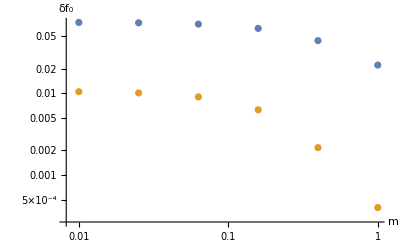
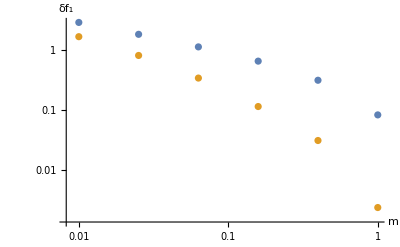

```mathematica
(*Plot the results*)
data0=Table[{ms[[l]],fres[[k,l,1]]},{k,Length[chis]},{l,Length[ms]}];data1=Table[{ms[[l]],fres[[k,l,2]]},{k,Length[chis]},{l,Length[ms]}];
Print[{ListLogLogPlot[data0,AxesLabel->{"m","δf_0"}],ListLogLogPlot[data1,AxesLabel->{"m","δf_1"}]}];
```